```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Needs["ThinLayer`","ThinLayer.m"]
```

```mathematica
x=Range[.1,2,.01];
L=Range[100,300,100];
```

```mathematica
(* MODEL INITIALIZATION *)
setlayer[ω_,lenrat_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2. 10^-5,cijPorous,cijFractured},
cijPorous=tlVTISquirtModuli[ϵ,0,α,τ,ω,0][λ,μ,ρ2,ϕ,kf];
cijFractured=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,cijPorous];
tlSetLayer[2,cijFractured];
]
```

```mathematica
setlayer[2Pi 25,100]
```

```mathematica
{freqvec,L100,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"../numerics/l100n0d500.mc","String"];
{freqvec,L200,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"../numerics/l200n0d500.mc","String"];
{freqvec,L300,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"../numerics/l300n0d500.mc","String"];
```

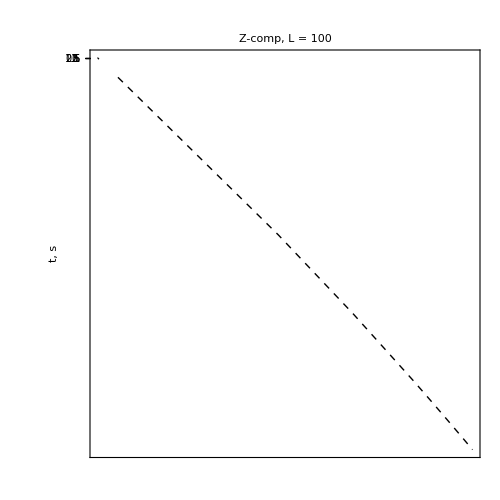
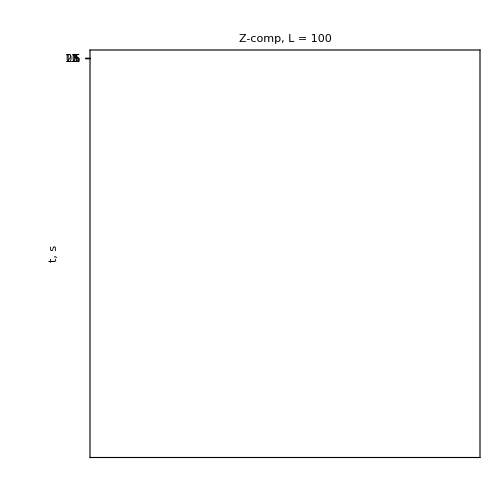
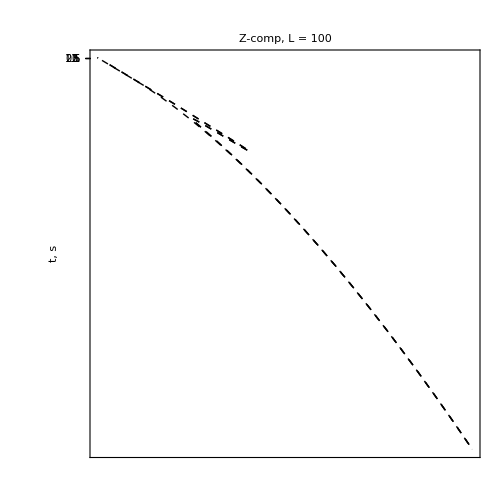
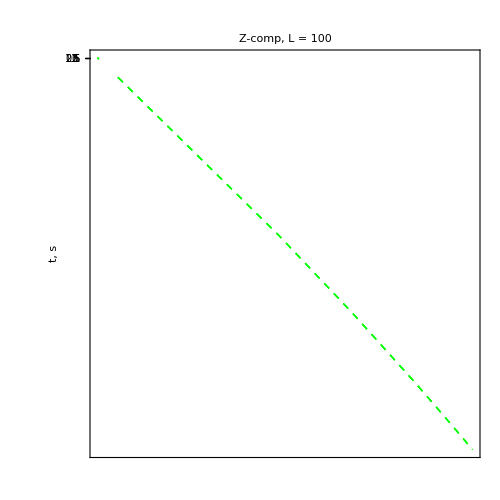
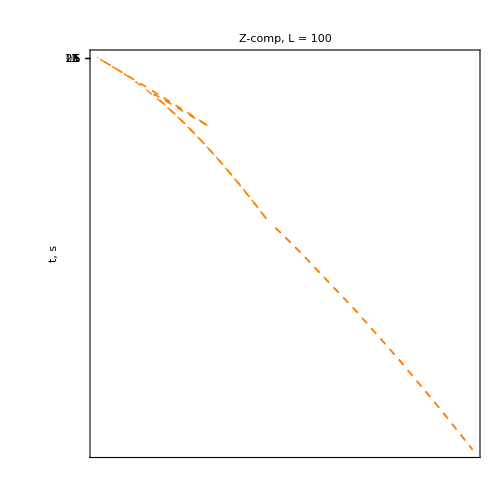
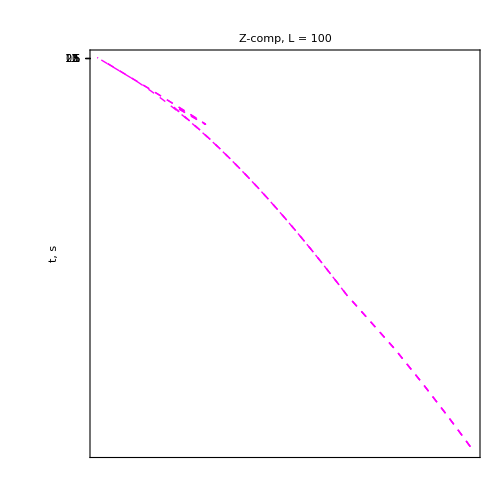
-Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
{{tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[1]]}],L100[[;;,1,;;]],freqvec,x,20,Abs@ωI,layers,depth,{.4,.8},0,50,2,"1S2SS1S"],
tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[1]]}],L100[[;;,1,;;]],freqvec,x,20,Abs@ωI,layers,depth,{.4,.8},0,50,2]}}//TableForm
```